```mathematica
Needs["ErrorBarPlots`"];
```

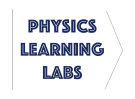
# -Graphics- Lab 10 - Black Hole Mass

In Prelab 10 we covered the background regarding physical observations of star S2 orbiting the putative black hole SgrA*. In this lab, we will plot the observational data and find the best fitting ellipse that describes S2’s orbital path. With our fitting parameters, we will be able to determine approximate mass of SgrA*, which we may then compare to published research estimates.

If you see the prompt “Do you want to automatically evaluate all the initialization cells in the notebook .. ?”, select Yes

## Experiment (Finding Orbital Period T)

### Plotting Observational Data

Recall the observational data gathered by astronomers over 10 years which measures the position of star S2 as it orbits SgrA*. Note the measurements are in units of arcsecs. In addition, dx and dy represent the uncertainty in angular distance, and thus may be graphically represented by error bars.

Date | x (arcsec) | dx (arcsec) | y (arcsec) | dy (arcsec)
1992.23 | 0.104 | 0.003 | -0.166 | 0.004
1994.32 | 0.097 | 0.003 | -0.189 | 0.004
1995.53 | 0.087 | 0.002 | -0.192 | 0.003
1996.26 | 0.075 | 0.007 | -0.197 | 0.01
1996.43 | 0.077 | 0.002 | -0.193 | 0.003
1997.54 | 0.052 | 0.004 | -0.183 | 0.006
1998.37 | 0.036 | 0.001 | -0.167 | 0.002
1999.47 | 0.022 | 0.004 | -0.156 | 0.006
2000.47 | 0. | 0.002 | -0.103 | 0.003
2000.52 | -0.013 | 0.003 | -0.113 | 0.004
2001.5 | -0.026 | 0.002 | -0.068 | 0.003
2002.25 | -0.013 | 0.005 | 0.003 | 0.007
2002.33 | -0.007 | 0.003 | 0.016 | 0.004
2002.41 | 0.009 | 0.003 | 0.023 | 0.005
2002.58 | 0.032 | 0.002 | 0.016 | 0.003
2002.65 | 0.037 | 0.002 | 0.009 | 0.003
2003.21 | 0.072 | 0.001 | -0.024 | 0.002
2003.35 | 0.077 | 0.002 | -0.03 | 0.002
2003.45 | 0.081 | 0.002 | -0.036 | 0.002

Our first task is to plot this observational data.

The observational data has conveniently been transcribed into a Mathematica table, stored as variable data below

```mathematica
data ={{1992.226,0.104,0.003,-0.166,0.004},{1994.321,0.097,0.003,-0.189,0.004},{1995.531,0.087,0.002,-0.192,0.003},{1996.256,0.075,0.007,-0.197,0.01},{1996.428,0.077,0.002,-0.193,0.003},{1997.543,0.052,0.004,-0.183,0.006},{1998.365,0.036,0.001,-0.167,0.002},{1999.465,0.022,0.004,-0.156,0.006},{2000.474,0.,0.002,-0.103,0.003},{2000.523,-0.013,0.003,-0.113,0.004},{2001.502,-0.026,0.002,-0.068,0.003},{2002.252,-0.013,0.005,0.003,0.007},{2002.334,-0.007,0.003,0.016,0.004},{2002.408,0.009,0.003,0.023,0.005},{2002.575,0.032,0.002,0.016,0.003},{2002.65,0.037,0.002,0.009,0.003},{2003.214,0.072,0.001,-0.024,0.002},{2003.353,0.077,0.002,-0.03,0.002},{2003.454,0.081,0.002,-0.036,0.002}};
```

To get our data into a form ready to be plotted, we have to make it compatible with the ErrorListPlot[] function. This step is completed within the variable finaldata

```mathematica
finaldata = Table[{{data[[i]][[2]],data[[i]][[4]]},ErrorBar[data[[i]][[3]],data[[i]][[5]]]},{i,1,Length[data]}];
```

```mathematica
Show[ErrorListPlot[finaldata],PlotRange->{{-.1,.17},{-.22,.05}},Axes->False,Frame->True,FrameLabel->{"x (arcsec)","y (arcsec)"}]
```

### Fitting Ellipse to Observational Data

We seek to find the semi-major axis of this ellipse. To find this, we may attempt to do a best fit of an ellipse to our data. Before we do this, we need to define some functions that orient our fit ellipse appropriately - specifically we must translate the origin and be able to rotate it by an angle θ. Shift-Enter below

```mathematica
origin = Mean[Table[finaldata[[i]][[1]],{i,1,Length[finaldata]}]];
xellipse[θ_,x_,y_]:= (x-origin[[1]])Cos[θ]-(y-origin[[2]])Sin[θ];
yellipse[θ_,x_,y_]:= (x-origin[[1]])Sin[θ]+(y-origin[[2]])Cos[θ];
```

If you forgot what the semi-major axis a and semi-minor axis b of an ellipse , here is a reminder:

In fitting the ellipse to the observational data, there are three parameters to adjust. The semi-minor axis b, the semi-major axis a, and angle θ. Use the sliders below to fit the ellipse to our data points. The black dot represents the location of the presumed black hole. A good fit minimizes the average of the distance between all data points and the fit line.

```mathematica
Manipulate[Show[ContourPlot[(xellipse[θ,x,y]/a)^2+(yellipse[θ,x,y]/b)^2==1,{x,-1,1},{y,-1,1},ContourStyle->Orange,PlotPoints->60],ErrorListPlot[finaldata],ListPlot[{{0,0}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}],PlotRange->{{-.1,.17},{-.22,.05}},Axes->False,Frame->True,FrameLabel->{"x (arcsec)","y (arcsec)"}],{{a,0.2},.01,.3,.005,Appearance->"Open"},{{b,0.04},.01,.12,.005,Appearance->"Open"},{{θ,2},0,2π,.01,Appearance->"Open"}]
```

Store your best fit values for the semi-major axis a and semi-minor axis b as variables below

```mathematica
afit = ;
bfit = ;
```

Using afit and bfit, calculate the total area of the ellipse and store within variable Aellipse below

```mathematica
Aellipse =  ;
```

### Finding ΔA/Δt

Recall that Kepler’s second law states that an object sweeps out equal areas over equal times: 
ΔA/Δt=const.	ΔA/Δt=A_ellipse/T

Since we already know A_ellipse, if we can find ΔA/Δt then we can measure the orbital period T of S2 as it orbits the black hole. How can we find ΔA/Δt? For simplicity, we can approximate the areas swept out by S2 between two observations by finding the area of a triangle with one point at the origin (0,0), and the other two points given as the data points in the table.

Based on the figure above, one triangle makes a much better approximate to the actual area than the other. Does the triangular approximation work better for shorter time intervals or longer time intervals? Why?

Given any three points in the x-y plane, the function below calculates the area of the respective triangle. Below, areadata takes our existing data and puts it into an appropriate format.

```mathematica
area[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=1/2Abs[x1 y2 + x2 y3 + x3 y1 - x2 y1 - x3 y2 - x1 y3]
```

```mathematica
areadata = Table[{data[[i]][[1]],{data[[i]][[2]],data[[i]][[4]]}},{i,1,Length[data]}];
```

Let’s find ΔA for each adjacent pair of observational data points

```mathematica
dA =Table[area[areadata[[i]][[2]],areadata[[i+1]][[2]],{0,0}],{i,1,Length[areadata]-1}]
```

We also want to calculate the respective Δt. The Table[] function below does this for us, calculating the time between each adjacent pair of points.

```mathematica
dt =Table[(areadata[[i+1]][[1]]-areadata[[i]][[1]]),{i,1,Length[areadata]-1}]
```

Now we need to divide each area by the time between adjacent points to give us ΔA/Δt. This is your list of ΔA/Δt values.

```mathematica
dAdt =Table[dA[[i]]/dt[[i]],{i,1,Length[areadata]-1}]
```

We could take Mean[dAdt] as this would give us an average value for ΔA/Δt. However, we know from the triangular ellipse figure that some triangles make very poor approximations compared to others. With this, it would make sense for us to attempt to filter out the areas that are poor approximations so that we can get a more accurate value of ΔA/Δt.

A clear way we could be selective about our data would be to plot the change in area ΔA vs the change in time Δt. Then we can fit a linear function that goes through the points that best approximate the true areas (remember this depends on whether data at shorter or longer time intervals make better approximations)

Use Manipulate to find the line that best approximates the true ΔA/Δt. Keep track of the resulting slope for the analysis.

```mathematica
Manipulate[Show[ListPlot[Table[{dt[[i]],dA[[i]]},{i,1,Length[dt]}]],Plot[m x,{x,0,2.2},PlotStyle->Black],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Δt (years)","ΔA (arcsec^2)"}],{m,0,.003,0.0001,Appearance->"Open"}]
```

With A_ellipse and ΔA/Δt now determined, we are able to calculate the orbital period T. This will be done in the analysis below.

## Analysis

Be sure to check that you have completed Q1 within subsection Finding ΔA/Δt

Paste a plot of the elliptical fit with observational data below

Comment on the quality of the fit to the observational data

Paste the graph of ΔA/Δt including the best fit line

State the values of the semi-major axis a, semi-minor axis b, ellipse area A_ellipse, and ΔA/Δt below. Show units.

SgrA* is approximately 26,000 ly (light years) away from Earth. Calculate the semi-major axis a in units of light days. (Refer to Prelab 10).

Using ΔA/Δt= A_ellipse/T, calculate the orbital period T of S2 in units of years. Your answer should lie near the range of 10-20 years.

Use Kepler’s third law T^2=a^3(4 π^2)/(G(M+m)) to find the total mass M+m in kg units. You may take the gravitational constant as G=7.838 x10^-44 ly^3 years^-2 kg^-1 or  G=6.674 x10^-11 m^3 s^-2 kg^-1 .

Given the mass of the sun M_s = 1.989 x10^30 kg, calculate the number of ‘sun-like’ stars that would be contained with the total mass M+m. This is equivalent to the mass of M+m in solar mass units.

Stars has masses that range from 0.08 to 120 solar masses. Given this information, how does the mass of a typical star compare to the total mass M+m? Are we justified in taking M>>m in Kepler’s third law?

We have determined the mass of the compact object of which the S2 is orbiting, but how do we know it is specifically a black hole? Maybe it is just a dense cluster of stars? Astronomers have determined that the amount of light coming from the ‘black hole’ area is significantly less than the amount of light in the surrounding the region. If SgrA* were composed of a cluster of stars, the luminosity would have to be VASTLY greater than what was observed. Thus it is fair to assume that the compact mass our star is gravitationally attracted to is indeed a black hole!

Open the research paper Schodel_Nature_SgrA.pdf. This is the published physics research paper that provided our observational data table for the orbit of S2 around SgrA*. Search through the paper and find the total mass physicists calculated for SgrA*, as well as the period for S2. State their results below.

Compare the nominal value of period and total mass from the research paper to your results from this lab. Does this fall within the uncertainty range provided in Schödel? If not, calculate the percent difference.

Which part of our procedure would you characterize as the most prone to error when calculating the black hole mass?

How does it feel to have calculated the mass of the supermassive black hole at the center of our galaxy with results that (if done properly) agree with published research?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).